# Code backup from March 1 2025

#### Rotation matrices applied to GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

```mathematica
(*visualizing matricies/ tensor*)
Rz[ϕ] //MatrixForm
P //MatrixForm
```

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

Applying the rotation matrix to all 3 polarizations. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

```mathematica
Simplify[Rz[ϕ].G.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ]-Sin[2 ϕ] | Cos[2 ϕ]+Sin[2 ϕ] | 0
Cos[2 ϕ]+Sin[2 ϕ] | -Cos[2 ϕ]+Sin[2 ϕ] | 0
0 | 0 | 0)

```mathematica
Simplify[Rz[ϕ].X.Transpose[Rz[ϕ]]] //MatrixForm
```

(-Sin[2 ϕ] | Cos[2 ϕ] | 0
Cos[2 ϕ] | Sin[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
Rx[α] //MatrixForm (*I think x should be by an angle α*)
Ry[α] //MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

(Cos[α] | 0 | Sin[α]
0 | 1 | 0
-Sin[α] | 0 | Cos[α])

#### Applying rotations:

Simplest case: Plus polarized wave rotated -α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].P.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(Cos[ϕ]^2-Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α]^2 Sin[ϕ] | -Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]
Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ] | -Cos[α]^2 Cos[ϕ] | Cos[α] Cos[ϕ]^2 Sin[α]-Sin[ϕ]^2
-Sin[α]^2 Sin[ϕ] | Cos[α] Sin[α] | -Cos[ϕ] Sin[α]^2)

The most complex case: GW with a general plus polarization p and cross polarisation x rotated α degrees about the x-axis and then ϕ degrees about the z-axis.

```mathematica
Simplify[Rz[ϕ].Rx[-α].G.Transpose[Rx[-α]].Transpose[Ry[ϕ]]] //MatrixForm
```

(p Cos[ϕ]^2-x Cos[ϕ] (Cos[α]+Sin[α]) Sin[ϕ]-p Cos[α] Sin[α] Sin[ϕ]^2 | Cos[α] (x Cos[ϕ]+p Cos[α] Sin[ϕ]) | -x Cos[ϕ]^2 Sin[α]-p Cos[ϕ] (1+Cos[α] Sin[α]) Sin[ϕ]+x Cos[α] Sin[ϕ]^2
Cos[α] Cos[ϕ] (x Cos[ϕ]+p Sin[α] Sin[ϕ])+Sin[ϕ] (p Cos[ϕ]-x Sin[α] Sin[ϕ]) | Cos[α] (-p Cos[α] Cos[ϕ]+x Sin[ϕ]) | -Sin[ϕ] (x Cos[ϕ] Sin[α]+p Sin[ϕ])+Cos[α] Cos[ϕ] (p Cos[ϕ] Sin[α]-x Sin[ϕ])
-Sin[α] (x Cos[ϕ]+p Sin[α] Sin[ϕ]) | p Cos[α] Sin[α] | Sin[α] (-p Cos[ϕ] Sin[α]+x Sin[ϕ]))

#### Other variables

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is recived
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP distance from GW source to photon
α angle between GW source and photon (measured up from GW propegation vector)
dP distance from Earth to the photon
tmin initial time the photon encounters the GW
n vector pointing to point on the sky where the photon is found

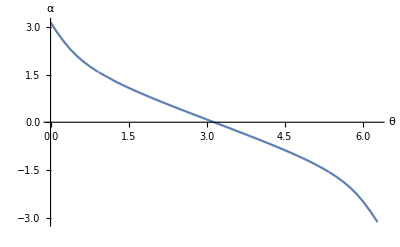

```mathematica
$Assumptions=dG>0&&h0>0&&tP>tG&&0<=θ<=2 π&&t∈Reals;
c= 1;
tG = 0;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] 
DP[tP_, t_] := c(tP-t) (*if tP > t*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP + 2 dG Cos[θ])
n[θ_] := {Sin[θ], 0, Cos[θ]}
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
Plot[A[5,3,θ], {θ,0,2π},AxesLabel->{"θ","α"}]
```

#### Metric in 2D simplification

Simplifying to 2D, in the plane of the Earth, GW source, and photon. Here, we are ignoring ϕ and only considering α.

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = Ε[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵ] //MatrixForm
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
H[t_, tP_, dG_, θ_] := 1/RP[dG,tP, t,θ] Ε[A[DP[tP,t], dG, θ]]
```

```mathematica
h = H[t,tP,dG,θ]; (*full expression for Subscript[h, ij], without multiplying by h0*)
```

```mathematica
FullSimplify[h] //MatrixForm
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

#### Simplifying metric representation

Simplifying Sin[2ArcTan[a/o]]

```mathematica
o = (-t+tP) Sin[θ];
a = dG+(t-tP) Cos[θ];
```

```mathematica
hyp = Sqrt[a^2+o^2]
```

√((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)

```mathematica
2*o/hyp*a/hyp (*Sin(2x) = 2CosxSinx*)
```

(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)

```mathematica
FullSimplify[(2 (-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG+(t-tP) Cos[θ])^2+(-t+tP)^2 Sin[θ]^2)] (*I graphed this against the original Sin[2ArcTan[]] and they look identical*)
```

-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
(-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) (*Simplifying the expression that appears in the matrix*)
```

-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 (-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {0, -1, 0}, {1/2 (-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}});
```

```mathematica
h= ({{(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}, {0, -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0}, {-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)), 0, ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))}});
```

Next steps
- Write up in methods section while checking all steps
- Test for a few specific cases 

- Solve for angular displacements

#### Redshift

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2))  (*taking the difference manually*)
```

-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)^(3/2))

```mathematica
FullSimplify[-1/2*(-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)^(3/2)))] (*full z expression*)
```

1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))

```mathematica
Z[θ_, dG_, tP_] := 1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))
```

```mathematica
Manipulate[PolarPlot[Z[θ,dG,tP] (*full z expression*),{θ,0,2 π}],{dG,0.1,2},{tP,0.1,2.5}]
```

z stabilizes when tP >> dG. The photon is received (measure after GW received) long after the light-travel time to the GW source.

```mathematica
FullSimplify[Z[θ,dG,tP]]
```

1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))

```mathematica
1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2-dG tP Cos[θ]+tP^2/4)^(3/2))) ;(*z when tP>>dG*)
```

```mathematica
Manipulate[PolarPlot[1/2 (Sin[θ]^2/dG-(dG^2 Sin[θ]^2)/((dG^2+tP^2/4-dG tP Cos[θ])^(3/2))),{θ,0,2 π}],{dG,0.01,3.604391290997247},{tP,0.01,3.604391290997247}]
```

```mathematica
zθMad = 1/4(1-Cos[θ]); (*Madison's equation for ϕ = 0*)
```

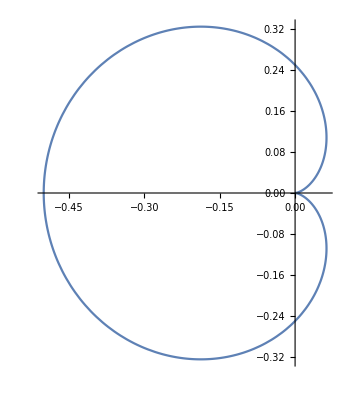

```mathematica
PolarPlot[zθMad,{θ,0,2 π}]
```

#### Other polarizations

Plus-polarized wave rotated through an angle ϕ

```mathematica
P //MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Rz[ϕ].P.Transpose[Rz[ϕ]] // MatrixForm
```

(Cos[ϕ]^2-Sin[ϕ]^2 | 2 Cos[ϕ] Sin[ϕ] | 0
2 Cos[ϕ] Sin[ϕ] | -Cos[ϕ]^2+Sin[ϕ]^2 | 0
0 | 0 | 0)

```mathematica
Εr[α_] := FullSimplify[Ry[-α].Rz[ϕ].P.Transpose[Rz[ϕ]].Transpose[Ry[-α]]] (*Polarization of a x GW at an angle α*)
Εr[α] //MatrixForm
```

(Cos[α]^2 Cos[2 ϕ] | Cos[α] Sin[2 ϕ] | Cos[α] Cos[2 ϕ] Sin[α]
Cos[α] Sin[2 ϕ] | -Cos[2 ϕ] | Sin[α] Sin[2 ϕ]
Cos[α] Cos[2 ϕ] Sin[α] | Sin[α] Sin[2 ϕ] | Cos[2 ϕ] Sin[α]^2)

```mathematica
ϵr = Εr[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵr] //MatrixForm
```

(((dG+(t-tP) Cos[θ])^2 Cos[2 ϕ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
Piecewise[{{-Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ϕ]/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | -Cos[2 ϕ] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
1/2 Cos[2 ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | Sin[2 ϕ] Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | ((t-tP)^2 Cos[2 ϕ] Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
intR = FullSimplify[n[θ].Transpose[n[θ].ϵr] *1/RP[dG,tP, t,θ]](*rotated integrand. applying n^i n^j and then applying 1/Rp*)
```

(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2)) ](*taking the difference manually*)
```

-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2))

```mathematica
Zr[θ_, ϕ_, dG_, tP_] := -1/2*(-(Cos[2 ϕ] Sin[θ]^2)/dG+(dG^2 Cos[2 ϕ] Sin[θ]^2)/((dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))^(3/2)))
```

```mathematica
Manipulate[SphericalPlot3D[Zr[θ, ϕ, dG, tP],{θ,0,π},{ϕ,0,2 π}, PlotRange->All],{dG,0.01,10.},{tP,0.01,10.}]
```

```mathematica
zMad = 1/4*2Cos[2ϕ]*(1-Cos[θ]); (*Madison's full equation*)
```

```mathematica
SphericalPlot3D[zMad,{θ,0,π},{ϕ,0,2 π}, PlotRange->All]
```

-Graphics3D-

Cross-polarized wave

```mathematica
X //MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a x GW at an angle α*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = Εx[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵx] //MatrixForm
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
Εx = ϵx*1/RP[dG,tP, t,θ];
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].Εx] ](*applying n^i n^j and then applying 1/Rp*)
```

0

Getting 0 for some reason?

#### Test integrating over ϵ

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 (-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {0, -1, 0}, {1/2 (-(2 (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}});
```

```mathematica
Subscript[ϵ, t] = D[ϵ,t];  (*time derivative of Subscript[ϵ, ij]*)
Subscript[ϵ, t] = FullSimplify[Subscript[ϵ, t]];
Subscript[ϵ, t] // MatrixForm
```

(-(2 dG (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | -(dG (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[2 θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | 0 | 0
-(dG (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[2 θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | (2 dG (t-tP) (dG+(t-tP) Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

```mathematica
FullSimplify[n[θ].Transpose[n[θ].Subscript[ϵ, t]]] (*applying n^i n^j*)
```

-(2 dG^2 (t-tP+dG Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)

```mathematica
Integrate[-(2 dG^2 (t-tP+dG Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2),{t,tP,Tmin[tG, tP, dG,θ]}] (*integration method*)
```

ConditionalExpression[(tP (2 dG (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP) (dG^2 (1+ⅇ^(ⅈ θ))^2 (1+ⅇ^(2 ⅈ θ))-2 dG ⅇ^(2 ⅈ θ) tP-ⅇ^(2 ⅈ θ) tP^2) Sin[θ]^2)/(dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4), ]

```mathematica
Integrate[-(2 dG^2 (t-tP+dG Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2),t]
```

(dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
FullSimplify[n[θ].Transpose[n[θ].ϵ]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
(dG^2 Sin[θ]^2)/(dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])-(dG^2 Sin[θ]^2)/(dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ]) (*difference applied manually*)
```

-Sin[θ]^2+(dG^2 Sin[θ]^2)/(dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)

```mathematica
FullSimplify[-Sin[θ]^2+(dG^2 Sin[θ]^2)/(dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)]
```

(-1+dG^2/(dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))) Sin[θ]^2

#### Calculating h integral 3 different ways (should be the same)

```mathematica
Subscript[h, t] = D[h,t];  (*time derivative of Subscript[ϵ, ij]*)
Subscript[h, t] = FullSimplify[Subscript[h, t]];
Subscript[h, t] // MatrixForm
```

(-((dG+(t-tP) Cos[θ]) (3 dG (t-tP)+Cos[θ] (dG^2+(t-tP)^2+dG (-t+tP) Cos[θ])))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)) | 0 | -((dG (dG^2-2 (t-tP)^2)+(t-tP) Cos[θ] ((dG+t-tP) (dG-t+tP)+dG (t-tP) Cos[θ])) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2))
0 | (t-tP+dG Cos[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0
-((dG (dG^2-2 (t-tP)^2)+(t-tP) Cos[θ] ((dG+t-tP) (dG-t+tP)+dG (t-tP) Cos[θ])) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)) | 0 | -((t-tP) (-2 dG^2+(t-tP)^2+dG (-t+tP) Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)))

```mathematica
FullSimplify[n[θ].Transpose[n[θ].Subscript[h, t]]] (*applying n^i n^j*)
```

-(3 dG^2 (t-tP+dG Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2))

```mathematica
Integrate[-(3 dG^2 (dG (dG^2+3 (t-tP)^2) Cos[θ]+(t-tP) (2 dG^2+(t-tP)^2+dG^2 Cos[2 θ])) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(7/2)),{t,tP,Tmin[tG, tP, dG,θ]}] (*integration method*)
```

```mathematica
Integrate[-(3 dG^2 (dG (dG^2+3 (t-tP)^2) Cos[θ]+(t-tP) (2 dG^2+(t-tP)^2+dG^2 Cos[2 θ])) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(7/2)),t]
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
NH[t_, tP_, dG_, θ_] := FullSimplify[n[θ].Transpose[n[θ].H[t,tP,dG,θ]]] (*applying n^i n^j in a function*)
```

```mathematica
NH[t,tP,dG,θ]
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
(dG^2 Sin[θ]^2)/((dG^2+(Tmin[tG, tP, dG,θ]-tP)^2+2 dG (Tmin[tG, tP, dG,θ]-tP) Cos[θ])^(3/2))-(dG^2 Sin[θ]^2)/((dG^2+(tP-tP)^2+2 dG (tP-tP) Cos[θ])^(3/2)) (*differnce, applied manually*)
```

-Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)^(3/2))

```mathematica
NH[Tmin[tG, tP, dG,θ], tP, dG, θ] - NH[tP, tP, dG, θ] (*difference of two functions*)
```

-Sin[θ]^2/(√(dG^2))+(2 Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))/(dG+tP+dG Cos[θ])^2))

#### Test without applying n^i n^j first

The three answers (should be the same, except int might be negative)

```mathematica
man = -Sin[θ]^2/(√(dG^2))+(dG^2 Sin[θ]^2)/((dG^2+2 dG Cos[θ] (-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))+(-tP+(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP+2 dG Cos[θ]))^2)^(3/2));
```

```mathematica
func = -Sin[θ]^2/(√(dG^2))+(2 Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))/(dG+tP+dG Cos[θ])^2));
```

```mathematica
int = (-tP^2-2 dG tP (1+Cos[θ])+dG^2 (1+2 Cos[θ]+Cos[2 θ])-Cos[θ] √(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]))/(√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]))
```

(-tP^2-2 dG tP (1+Cos[θ])+dG^2 (1+2 Cos[θ]+Cos[2 θ])-Cos[θ] √(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]))/(√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]))

Metric difference

```mathematica
hi = H[Tmin[0, tP, dG,θ],tP,dG,θ];
hf =  H[tP,tP,dG,θ];
```

```mathematica
diff = Simplify[hi-hf];
```

```mathematica
diff //MatrixForm
```

(-1/(√(dG^2))+(2 ((2 dG^2-2 dG tP-tP^2) Cos[θ]+2 dG (dG-tP Cos[2 θ]))^2)/((dG+tP+dG Cos[θ])^2 ((6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ])/(dG+tP+dG Cos[θ])^2)^(3/2)) | 0 | Piecewise[{{-(Sin[2 ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG (2 dG^3+dG tP^2+tP^3) Cos[θ]+4 dG^2 (dG^2-6 dG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)/(dG+tP+dG Cos[θ])^2))), ((2 dG^2-tP^2+2 dG (dG-2 tP) Cos[θ])/(dG+tP+dG Cos[θ])≥0&&θ≤0)||(dG ((4 dG^2-2 dG tP-5 tP^2) Cos[θ]+dG (3 dG+(dG-2 tP) Cos[2 θ]))<tP^2 (dG+tP)&&θ≤ArcCos[(2 dG (dG+tP+dG Cos[θ]))/(tP (2 dG+tP+4 dG Cos[θ]))])}, {Sin[2 ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((2 dG^2-2 dG tP-tP^2) Cos[θ]+2 dG (dG-tP Cos[2 θ]))]]/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG (2 dG^3+dG tP^2+tP^3) Cos[θ]+4 dG^2 (dG^2-6 dG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)/(dG+tP+dG Cos[θ])^2)), True}}]
0 | 1/(√(dG^2))-1/(√(dG^2-(dG tP Cos[θ] (2 dG+tP+4 dG Cos[θ]))/(dG+tP+dG Cos[θ])+(tP^2 (2 dG+tP+4 dG Cos[θ])^2)/(4 (dG+tP+dG Cos[θ])^2))) | 0
Piecewise[{{-(Sin[2 ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG (2 dG^3+dG tP^2+tP^3) Cos[θ]+4 dG^2 (dG^2-6 dG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)/(dG+tP+dG Cos[θ])^2))), ((2 dG^2-tP^2+2 dG (dG-2 tP) Cos[θ])/(dG+tP+dG Cos[θ])≥0&&θ≤0)||(dG ((4 dG^2-2 dG tP-5 tP^2) Cos[θ]+dG (3 dG+(dG-2 tP) Cos[2 θ]))<tP^2 (dG+tP)&&θ≤ArcCos[(2 dG (dG+tP+dG Cos[θ]))/(tP (2 dG+tP+4 dG Cos[θ]))])}, {Sin[2 ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((2 dG^2-2 dG tP-tP^2) Cos[θ]+2 dG (dG-tP Cos[2 θ]))]]/(√(((2 dG^2+2 dG tP+tP^2)^2+4 dG (2 dG^3+dG tP^2+tP^3) Cos[θ]+4 dG^2 (dG^2-6 dG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)/(dG+tP+dG Cos[θ])^2)), True}}] | 0 | (2 tP^2 (2 dG+tP+4 dG Cos[θ])^2 Sin[θ]^2)/((dG+tP+dG Cos[θ])^2 ((6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ])/(dG+tP+dG Cos[θ])^2)^(3/2)))

```mathematica
FullSimplify[n[θ].Transpose[n[θ].diff]]
```

(-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2+2 dG Abs[dG+tP+dG Cos[θ]] Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(dG √((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))))

```mathematica
thm = (-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2+2 dG Abs[dG+tP+dG Cos[θ]] Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(dG √((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))))
```

(-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2+2 dG Abs[dG+tP+dG Cos[θ]] Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(dG √((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))))

#### Testing integration for redshift

```mathematica
Subscript[h, t] = D[h,t] ; (*time derivative of Subscript[h, ij]*)
FullSimplify[Subscript[h, t]] //MatrixForm
```

(-((dG+(t-tP) Cos[θ]) (3 dG (t-tP)+Cos[θ] (dG^2+(t-tP)^2+dG (-t+tP) Cos[θ])))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)) | 0 | (-2 dG Cos[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] Sin[θ]+(t-tP+dG Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | (t-tP+dG Cos[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0
(-2 dG Cos[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] Sin[θ]+(t-tP+dG Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -((t-tP) (-2 dG^2+(t-tP)^2+dG (-t+tP) Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)))

```mathematica
(*Integrate[h',{t,Tmin[tG, tP, dG,θ],tP}]*)
```

```mathematica
test = -(h0 (dG+(t-tP) Cos[θ]) (3 dG (t-tP)+Cos[θ] (dG^2+(t-tP)^2+dG (-t+tP) Cos[θ])))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2));
```

```mathematica
Integrate[test,{t,Tmin[tG, tP, dG,θ],tP}]
```

ConditionalExpression[-h0 (-1/(√(dG^2))+(dG-tP Cos[θ]+(Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2/(dG^2+tP^2-2 dG tP Cos[θ]-(2 tP (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+(2 dG Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+((2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])^2)/(2 dG-2 tG+2 tP+2 dG Cos[θ])^2)^(3/2)), ]

```mathematica
tG = 0 (*it was faster to evaluate when tG = 0*)
FullSimplify[- (-1/(√(dG^2))+(dG-tP Cos[θ]+(Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2/(dG^2+tP^2-2 dG tP Cos[θ]-(2 tP (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+(2 dG Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+((2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])^2)/(2 dG-2 tG+2 tP+2 dG Cos[θ])^2)^(3/2))]
```

1/dG-(2 (dG+tP+dG Cos[θ]) ((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))^2)/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2))

```mathematica
xx=1/dG-(2 (dG+tP+dG Cos[θ]) ((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))^2)/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2));
```

```mathematica
Clear[tG] (*this was slower to evaluate *)
```

```mathematica
FullSimplify[- (-1/(√(dG^2))+(dG-tP Cos[θ]+(Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2/(dG^2+tP^2-2 dG tP Cos[θ]-(2 tP (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+(2 dG Cos[θ] (2 dG tG-tG^2+tP^2-2 dG tP Cos[θ]))/(2 dG-2 tG+2 tP+2 dG Cos[θ])+((2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])^2)/(2 dG-2 tG+2 tP+2 dG Cos[θ])^2)^(3/2))]
```

1/dG-(8 (dG+(Cos[θ] ((tG-tP) (2 dG-tG+tP)-4 dG tP Cos[θ]))/(2 (dG-tG+tP+dG Cos[θ])))^2)/((((2 dG^2+(tG-tP)^2+2 dG (-tG+tP))^2+4 dG Cos[θ] (2 dG^3+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)-dG Cos[θ] (-dG^2-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2+4 dG tP Cos[θ])))/(dG-tG+tP+dG Cos[θ])^2)^(3/2))

Evaluating each h_ij entry separately for tG = 0

```mathematica
Integrate[(h0 (t-tP+dG Cos[θ]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)),{t,Tmin[0, tP, dG,θ],tP}] (*sets tG = 0*)
```

ConditionalExpression[h0 (((dG^3 √(dG^2)+2 dG^3 √(dG^2) ⅇ^(ⅈ θ)+dG^3 √(dG^2) ⅇ^(2 ⅈ θ)+2 (dG^2)^(3/2) ⅇ^(ⅈ θ) tP-2 (dG^2)^(3/2) (1+ⅇ^(2 ⅈ θ)) tP+2 dG √(dG^2) tP^2+2 dG √(dG^2) ⅇ^(ⅈ θ) tP^2+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP^2+√(dG^2) ⅇ^(ⅈ θ) tP^3-3 (dG^2)^(3/2) tP Cos[θ]-3 (dG^2)^(3/2) ⅇ^(2 ⅈ θ) tP Cos[θ]-3 dG √(dG^2) ⅇ^(ⅈ θ) tP^2 Cos[θ]-dG^3 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-2 dG^3 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-dG^3 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-2 dG^2 ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 (1+ⅇ^(2 ⅈ θ)) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG (1+ⅇ^(2 ⅈ θ)) tP^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 tP Cos[θ] √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 ⅇ^(2 ⅈ θ) tP Cos[θ] √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])) Csc[θ]^2)/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))+(dG Cot[θ] (-(dG^2)^(3/2) Cot[θ]-2 (dG^2)^(3/2) ⅇ^(ⅈ θ) Cot[θ]-(dG^2)^(3/2) ⅇ^(2 ⅈ θ) Cot[θ]-2 dG √(dG^2) ⅇ^(ⅈ θ) tP Cot[θ]+dG^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG^2 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+dG^2 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG √(dG^2) tP Csc[θ]+2 dG √(dG^2) ⅇ^(ⅈ θ) tP Csc[θ]+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP Csc[θ]+√(dG^2) ⅇ^(ⅈ θ) tP^2 Csc[θ]))/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))-(tP Csc[θ] (-(dG^2)^(3/2) Cot[θ]-2 (dG^2)^(3/2) ⅇ^(ⅈ θ) Cot[θ]-(dG^2)^(3/2) ⅇ^(2 ⅈ θ) Cot[θ]-2 dG √(dG^2) ⅇ^(ⅈ θ) tP Cot[θ]+dG^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG^2 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+dG^2 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG √(dG^2) tP Csc[θ]+2 dG √(dG^2) ⅇ^(ⅈ θ) tP Csc[θ]+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP Csc[θ]+√(dG^2) ⅇ^(ⅈ θ) tP^2 Csc[θ]))/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))), ]

```mathematica
FullSimplify[ConditionalExpression[h0 (((dG^3 √(dG^2)+2 dG^3 √(dG^2) ⅇ^(ⅈ θ)+dG^3 √(dG^2) ⅇ^(2 ⅈ θ)+2 (dG^2)^(3/2) ⅇ^(ⅈ θ) tP-2 (dG^2)^(3/2) (1+ⅇ^(2 ⅈ θ)) tP+2 dG √(dG^2) tP^2+2 dG √(dG^2) ⅇ^(ⅈ θ) tP^2+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP^2+√(dG^2) ⅇ^(ⅈ θ) tP^3-3 (dG^2)^(3/2) tP Cos[θ]-3 (dG^2)^(3/2) ⅇ^(2 ⅈ θ) tP Cos[θ]-3 dG √(dG^2) ⅇ^(ⅈ θ) tP^2 Cos[θ]-dG^3 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-2 dG^3 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-dG^3 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])-2 dG^2 ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 (1+ⅇ^(2 ⅈ θ)) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG (1+ⅇ^(2 ⅈ θ)) tP^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 tP Cos[θ] √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])+dG^2 ⅇ^(2 ⅈ θ) tP Cos[θ] √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])) Csc[θ]^2)/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))+(dG Cot[θ] (-(dG^2)^(3/2) Cot[θ]-2 (dG^2)^(3/2) ⅇ^(ⅈ θ) Cot[θ]-(dG^2)^(3/2) ⅇ^(2 ⅈ θ) Cot[θ]-2 dG √(dG^2) ⅇ^(ⅈ θ) tP Cot[θ]+dG^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG^2 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+dG^2 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG √(dG^2) tP Csc[θ]+2 dG √(dG^2) ⅇ^(ⅈ θ) tP Csc[θ]+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP Csc[θ]+√(dG^2) ⅇ^(ⅈ θ) tP^2 Csc[θ]))/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))-(tP Csc[θ] (-(dG^2)^(3/2) Cot[θ]-2 (dG^2)^(3/2) ⅇ^(ⅈ θ) Cot[θ]-(dG^2)^(3/2) ⅇ^(2 ⅈ θ) Cot[θ]-2 dG √(dG^2) ⅇ^(ⅈ θ) tP Cot[θ]+dG^2 √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG^2 ⅇ^(ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+dG^2 ⅇ^(2 ⅈ θ) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG ⅇ^(ⅈ θ) tP √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]) Cot[θ]+2 dG √(dG^2) tP Csc[θ]+2 dG √(dG^2) ⅇ^(ⅈ θ) tP Csc[θ]+2 dG √(dG^2) ⅇ^(2 ⅈ θ) tP Csc[θ]+√(dG^2) ⅇ^(ⅈ θ) tP^2 Csc[θ]))/((dG^2)^(3/2) (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ]))), ]]
```

```mathematica
ConditionalExpression[-h0/dG+(2 h0 Abs[dG+tP+dG Cos[θ]])/(√((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))), ]
```

```mathematica
yy = ConditionalExpression[-h0/dG+(2 h0 Abs[dG+tP+dG Cos[θ]])/(√((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))), ];
```

```mathematica
Integrate[-(h0 (t-tP) (-2 dG^2+(t-tP)^2+dG (-t+tP) Cos[θ]) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(5/2)),{t,Tmin[0, tP, dG,θ],tP}] (*sets tG = 0*)
```

ConditionalExpression[-((h0 tP^2 (2 dG (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)^2 Sin[θ]^2)/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2 (1/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2)ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))^(3/2))), ]

```mathematica
zz = ConditionalExpression[-((h0 tP^2 (2 dG (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)^2 Sin[θ]^2)/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2 (1/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2)ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))^(3/2))), ];
```

```mathematica
Integrate[(-2 dG h0 Cos[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] Sin[θ]+h0 (t-tP+dG Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)),{t,Tmin[0, tP, dG,θ],tP}](*sets tG = 0*)
```

ConditionalExpression[(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) h0 tP (-4 dG^3 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+2 dG^2 (1+ⅇ^(ⅈ θ))^2 (2+ⅇ^(2 ⅈ θ)+2 ⅇ^(4 ⅈ θ)) tP+4 dG ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)) tP^2+(ⅇ^(2 ⅈ θ)+ⅇ^(4 ⅈ θ)) tP^3))/(4 (-dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4+2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP+dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2-2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3-ⅇ^(3 ⅈ θ) tP^4) √(1/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2)ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))), ]

```mathematica
FullSimplify[ConditionalExpression[(ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) h0 tP (-4 dG^3 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+2 dG^2 (1+ⅇ^(ⅈ θ))^2 (2+ⅇ^(2 ⅈ θ)+2 ⅇ^(4 ⅈ θ)) tP+4 dG ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)) tP^2+(ⅇ^(2 ⅈ θ)+ⅇ^(4 ⅈ θ)) tP^3))/(4 (-dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4+2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP+dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2-2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3-ⅇ^(3 ⅈ θ) tP^4) √(1/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2)ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))), ]]
```

ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2), ]

```mathematica
xz = ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2), ]'
```

ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2), ]'

```mathematica
Mint = ({{xx, 0, xz}, {0, yy, 0}, {xz, 0, zz}});
Mint //MatrixForm
```

(1/dG-(2 (dG+tP+dG Cos[θ]) ((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))^2)/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2)) | 0 | ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2)), ]'
0 | ConditionalExpression[-h0/dG+(2 h0 Abs[dG+tP+dG Cos[θ]])/(√((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))), ] | 0
ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2)), ]' | 0 | ConditionalExpression[-((h0 tP^2 (2 dG (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)^2 Sin[θ]^2)/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2 ((ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2))^(3/2))), ])

```mathematica
int = Simplify[n[θ].Transpose[n[θ].Mint]]
```

ConditionalExpression[Sin[θ] ((1/dG-(2 (dG+tP+dG Cos[θ]) ((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))^2)/(((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2))) Sin[θ]+Cos[θ] ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2), ]'+Cos[θ] (-(h0 tP^2 (2 dG (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)^2 Cos[θ] Sin[θ])/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2 ((ⅇ^(-ⅈ θ) (dG^4 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^4-2 dG^3 (1+ⅇ^(ⅈ θ))^4 (1-ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP-dG^2 ⅇ^(ⅈ θ) (1+ⅇ^(ⅈ θ))^2 (1-4 ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)) tP^2+2 dG ⅇ^(2 ⅈ θ) (1+ⅇ^(ⅈ θ))^2 tP^3+ⅇ^(3 ⅈ θ) tP^4))/((dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)^2))^(3/2))+ConditionalExpression[(2 h0 tP Abs[dG+tP+dG Cos[θ]] ((-12 dG^3+6 dG^2 tP+4 dG tP^2+tP^3) Cos[θ]+2 dG (-4 dG^2+dG tP+tP^2+2 (-dG^2+2 dG tP+tP^2) Cos[2 θ]+2 dG tP Cos[3 θ])) Sin[θ])/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ])))^(3/2), ]')), ]

```mathematica
int = FullSimplify[int]
```

```mathematica
thm  (*should equal int, but calculated using fund. thm of calculus*)
```

(-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2+2 dG Abs[dG+tP+dG Cos[θ]] Sin[θ-ArcTan[(tP (2 dG+tP+4 dG Cos[θ]) Sin[θ])/((-2 dG^2+2 dG tP+tP^2) Cos[θ]-2 dG (dG-tP Cos[2 θ]))]]^2)/(dG √((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))))

#### Non-decreasing GW front

(I forgot to divide by Rp) α was also not properly defined because I forgot to +/- π

```mathematica
ϵ = Ε[A[DP[tP,t], dG, θ]]; (*plugging in α*)
FullSimplify[ϵ] //MatrixForm
```

(1/(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
ϵi = Ε[A[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ]]; (*plugging in α*)
FullSimplify[ϵi] //MatrixForm
```

(1/(1+((tG-tP) (-2 dG+tG-tP) Sin[θ]+2 dG tP Sin[2 θ])^2/(((-2 dG^2+(tG-tP)^2+2 dG (-tG+tP)) Cos[θ]+2 dG (-dG+tG+tP Cos[2 θ]))^2)) | 0 | (((tG-tP) (-2 dG+tG-tP)+4 dG tP Cos[θ]) Sin[θ])/(2 (dG-tG+tP+dG Cos[θ]) (dG+(Cos[θ] ((tG-tP) (2 dG-tG+tP)-4 dG tP Cos[θ]))/(2 (dG-tG+tP+dG Cos[θ]))) (1+((tG-tP) (-2 dG+tG-tP) Sin[θ]+2 dG tP Sin[2 θ])^2/(((-2 dG^2+(tG-tP)^2+2 dG (-tG+tP)) Cos[θ]+2 dG (-dG+tG+tP Cos[2 θ]))^2)))
0 | -1 | 0
(((tG-tP) (-2 dG+tG-tP)+4 dG tP Cos[θ]) Sin[θ])/(2 (dG-tG+tP+dG Cos[θ]) (dG+(Cos[θ] ((tG-tP) (2 dG-tG+tP)-4 dG tP Cos[θ]))/(2 (dG-tG+tP+dG Cos[θ]))) (1+((tG-tP) (-2 dG+tG-tP) Sin[θ]+2 dG tP Sin[2 θ])^2/(((-2 dG^2+(tG-tP)^2+2 dG (-tG+tP)) Cos[θ]+2 dG (-dG+tG+tP Cos[2 θ]))^2))) | 0 | 1/(1+(((-2 dG^2+(tG-tP)^2+2 dG (-tG+tP)) Cot[θ]+2 dG (-dG+tG+tP Cos[2 θ]) Csc[θ])^2)/((tG-tP) (2 dG-tG+tP)-4 dG tP Cos[θ])^2))

```mathematica
ϵf = Ε[A[0, dG, θ]]; (*plugging in α*)
FullSimplify[ϵf] //MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
ϵi - ϵf
```

{{-1+1/(1+((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2 Sin[θ]^2)/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])))^2)),0,((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])) Sin[θ])/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))) (1+((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2 Sin[θ]^2)/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])))^2)))},{0,0,0},{((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])) Sin[θ])/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))) (1+((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2 Sin[θ]^2)/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])))^2))),0,((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2 Sin[θ]^2)/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])))^2 (1+((tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ]))^2 Sin[θ]^2)/((dG-Cos[θ] (tP-(2 dG tG-tG^2+tP^2-2 dG tP Cos[θ])/(2 dG-2 tG+2 tP+2 dG Cos[θ])))^2)))}}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].(ϵf - ϵi)]] // MatrixForm
```

((4 dG^3 (tG-3 tP)-4 dG (tG-tP)^3+(tG-tP)^4+2 dG^2 (tG+tP)^2+4 dG (dG^2 (2 tG-5 tP)+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]-2 dG^2 (-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/(6 dG^4-4 dG (tG-tP)^3+(tG-tP)^4-4 dG^3 (tG+tP)+dG^2 (6 tG^2-4 tG tP+6 tP^2)+4 dG (2 dG^3-3 dG^2 tP+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]+2 dG^2 ((dG^2+2 dG tG-tG^2-6 dG tP+6 tG tP-tP^2) Cos[2 θ]-2 dG tP Cos[3 θ]))

```mathematica
ϵdif = ((4 dG^3 (tG-3 tP)-4 dG (tG-tP)^3+(tG-tP)^4+2 dG^2 (tG+tP)^2+4 dG (dG^2 (2 tG-5 tP)+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]-2 dG^2 (-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/(6 dG^4-4 dG (tG-tP)^3+(tG-tP)^4-4 dG^3 (tG+tP)+dG^2 (6 tG^2-4 tG tP+6 tP^2)+4 dG (2 dG^3-3 dG^2 tP+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]+2 dG^2 ((dG^2+2 dG tG-tG^2-6 dG tP+6 tG tP-tP^2) Cos[2 θ]-2 dG tP Cos[3 θ]))
```

((-12 dG^3 tP+2 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (-5 dG^2 tP+dG tP^2+tP^3) Cos[θ]-2 dG^2 (6 dG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 ((dG^2-6 dG tP-tP^2) Cos[2 θ]-2 dG tP Cos[3 θ]))

```mathematica
e
```

ConditionalExpression[((-12 dG^3 tP+2 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (-5 dG^2 tP+dG tP^2+tP^3) Cos[θ]-2 dG^2 (6 dG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))), ]

```mathematica
Expand[6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 ((dG^2-6 dG tP-tP^2) Cos[2 θ]-2 dG tP Cos[3 θ])]
```

6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+8 dG^4 Cos[θ]-12 dG^3 tP Cos[θ]+4 dG^2 tP^2 Cos[θ]+4 dG tP^3 Cos[θ]+2 dG^4 Cos[2 θ]-12 dG^3 tP Cos[2 θ]-2 dG^2 tP^2 Cos[2 θ]-4 dG^3 tP Cos[3 θ]

```mathematica
Expand[(2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))]
```

4 dG^4+8 dG^3 tP+8 dG^2 tP^2+4 dG tP^3+tP^4+8 dG^4 Cos[θ]+4 dG^2 tP^2 Cos[θ]+4 dG tP^3 Cos[θ]+4 dG^4 Cos[θ]^2-24 dG^3 tP Cos[θ]^2-4 dG^2 tP^2 Cos[θ]^2-16 dG^3 tP Cos[θ]^3

```mathematica
(*compare the 2 above Cos[2x] and Cos[3x]*)
```

```mathematica
ζ
```

ConditionalExpression[((4 dG^3 (tG-3 tP)-4 dG (tG-tP)^3+(tG-tP)^4+2 dG^2 (tG+tP)^2+4 dG (dG^2 (2 tG-5 tP)+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]-2 dG^2 (-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/((2 dG^2+(tG-tP)^2+2 dG (-tG+tP))^2+4 dG Cos[θ] (2 dG^3+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)-dG Cos[θ] (-dG^2-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2+4 dG tP Cos[θ]))), ]

```mathematica
tG = 0
```

0

```mathematica
FullSimplify[((2 dG^2+(tG-tP)^2+2 dG (-tG+tP))^2+4 dG Cos[θ] (2 dG^3+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)-dG Cos[θ] (-dG^2-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2+4 dG tP Cos[θ])))]
```

(2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))

```mathematica
Expand[(2 dG^2+2 dG tP+tP^2)^2+4 dG Cos[θ] (2 dG^3+dG tP^2+tP^3-dG Cos[θ] (-dG^2+6 dG tP+tP^2+4 dG tP Cos[θ]))]
```

4 dG^4+8 dG^3 tP+8 dG^2 tP^2+4 dG tP^3+tP^4+8 dG^4 Cos[θ]+4 dG^2 tP^2 Cos[θ]+4 dG tP^3 Cos[θ]+4 dG^4 Cos[θ]^2-24 dG^3 tP Cos[θ]^2-4 dG^2 tP^2 Cos[θ]^2-16 dG^3 tP Cos[θ]^3

```mathematica
FullSimplify[(6 dG^4-4 dG (tG-tP)^3+(tG-tP)^4-4 dG^3 (tG+tP)+dG^2 (6 tG^2-4 tG tP+6 tP^2)+4 dG (2 dG^3-3 dG^2 tP+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]+2 dG^2 ((dG^2+2 dG tG-tG^2-6 dG tP+6 tG tP-tP^2) Cos[2 θ]-2 dG tP Cos[3 θ]))]
```

6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]

```mathematica
Expand[6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]]
```

6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+8 dG^4 Cos[θ]-12 dG^3 tP Cos[θ]+4 dG^2 tP^2 Cos[θ]+4 dG tP^3 Cos[θ]+2 dG^4 Cos[2 θ]-12 dG^3 tP Cos[2 θ]-2 dG^2 tP^2 Cos[2 θ]-4 dG^3 tP Cos[3 θ]

```mathematica
Tint = {{ConditionalExpression[-2 dG (-1/(2 dG)+(2 (dG-tG+tP+dG Cos[θ]) (dG (dG-tG+tP)+(dG^2+2 dG (tG-tP)-(tG-tP)^2) Cos[θ]-4 dG tP Cos[θ]^2))/((2 dG^2-2 dG (tG-tP)+(tG-tP)^2)^2+4 dG (2 dG^3+(tG-tP)^2 (tG+tP)+dG (-3 tG^2+2 tG tP+tP^2)) Cos[θ]+4 dG^2 (dG^2-tG^2+2 dG (tG-3 tP)+6 tG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)) Sin[θ]^2, ],0,ConditionalExpression[-dG (-Cos[θ]/dG+(2 (dG-tG+tP+dG Cos[θ]) (2 dG (dG-tG) Cos[θ]+(dG^2+2 dG (tG-tP)-(tG-tP)^2) Cos[2 θ]+dG (dG-2 tP Cos[3 θ])))/((2 dG^2-2 dG (tG-tP)+(tG-tP)^2)^2+4 dG (2 dG^3+(tG-tP)^2 (tG+tP)+dG (-3 tG^2+2 tG tP+tP^2)) Cos[θ]+4 dG^2 (dG^2-tG^2+2 dG (tG-3 tP)+6 tG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)) Sin[θ], ]},{0,0,0},{ConditionalExpression[-dG (-Cos[θ]/dG+(2 (dG-tG+tP+dG Cos[θ]) (2 dG (dG-tG) Cos[θ]+(dG^2+2 dG (tG-tP)-(tG-tP)^2) Cos[2 θ]+dG (dG-2 tP Cos[3 θ])))/((2 dG^2-2 dG (tG-tP)+(tG-tP)^2)^2+4 dG (2 dG^3+(tG-tP)^2 (tG+tP)+dG (-3 tG^2+2 tG tP+tP^2)) Cos[θ]+4 dG^2 (dG^2-tG^2+2 dG (tG-3 tP)+6 tG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)) Sin[θ], ],0,ConditionalExpression[2 dG (-1/(2 dG)+(2 (dG-tG+tP+dG Cos[θ]) (dG (dG-tG+tP)+(dG^2+2 dG (tG-tP)-(tG-tP)^2) Cos[θ]-4 dG tP Cos[θ]^2))/((2 dG^2-2 dG (tG-tP)+(tG-tP)^2)^2+4 dG (2 dG^3+(tG-tP)^2 (tG+tP)+dG (-3 tG^2+2 tG tP+tP^2)) Cos[θ]+4 dG^2 (dG^2-tG^2+2 dG (tG-3 tP)+6 tG tP-tP^2) Cos[θ]^2-16 dG^3 tP Cos[θ]^3)) Sin[θ]^2, ]}};
```

```mathematica
FullSimplify[n[θ].Transpose[n[θ].int]] // MatrixForm
```

ConditionalExpression[((4 dG^3 (tG-3 tP)-4 dG (tG-tP)^3+(tG-tP)^4+2 dG^2 (tG+tP)^2+4 dG (dG^2 (2 tG-5 tP)+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]-2 dG^2 (-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/((2 dG^2+(tG-tP)^2+2 dG (-tG+tP))^2+4 dG Cos[θ] (2 dG^3+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)-dG Cos[θ] (-dG^2-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2+4 dG tP Cos[θ]))), ]

```mathematica
e = ConditionalExpression[((4 dG^3 (tG-3 tP)-4 dG (tG-tP)^3+(tG-tP)^4+2 dG^2 (tG+tP)^2+4 dG (dG^2 (2 tG-5 tP)+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)) Cos[θ]-2 dG^2 (-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ]) Sin[θ]^2)/((2 dG^2+(tG-tP)^2+2 dG (-tG+tP))^2+4 dG Cos[θ] (2 dG^3+(tG-tP)^2 (tG+tP)-dG (tG-tP) (3 tG+tP)-dG Cos[θ] (-dG^2-2 dG tG+tG^2+6 dG tP-6 tG tP+tP^2+4 dG tP Cos[θ]))), ];
```

z = ζ 1/2. The negative cancels out since we use opposite integral bounds. I don’t know what to do about ω_0 but I think it drops out when converting the integral over dλ to dt, dλ = dt/ω_0? 
ζ is directly proportional to Sin[θ]^2, meaning it is 0 for small θ. 
A simplifying assumption we may be able to make is that dG is small. This is the distance to the gravitational wave source.

### Deflection angle

```mathematica
FullSimplify[h] //MatrixForm
```

(1/(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
Subscript[h, x]= D[DP[tP,t]Cos[θ] h,θ] ; (*x = dP Sin[θ] so dx = dP Cos[θ] dθ ?*) (*check Rp versus dp!!*)
Subscript[h, y]=0 ; 
Subscript[h, z]= D[-DP[tP,t]Sin[θ] h,θ] ; (*z = dP Cos[θ] so dz = -dP Sin[θ] dθ ?*)
FullSimplify[Subscript[h, x]] //MatrixForm
FullSimplify[Subscript[h, z]] //MatrixForm
```

(((t-tP) (dG+(t-tP) Cos[θ]) (3 (dG^2+(t-tP)^2) (t-tP) Cos[θ]+dG (dG^2+3 (t-tP)^2+2 (t-tP)^2 Cos[2 θ])) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Sin[θ] | 0
((t-tP)^2 ((7 dG^2+(t-tP)^2) (t-tP) Cos[θ]+4 dG Cos[2 θ] (dG^2+2 (t-tP)^2+(t-tP)^2 Cos[2 θ])+(5 dG^2+3 (t-tP)^2) (t-tP) Cos[3 θ]))/(4 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | -((t-tP)^3 (6 dG (t-tP) Cos[θ]+(dG^2+(t-tP)^2) (1+3 Cos[2 θ])+2 dG (t-tP) Cos[3 θ]) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

(((t-tP) (Cos[θ]+((t-tP)^2 (-2 t+2 tP-dG Cos[θ]+(t-tP) Cos[θ]^2) Sin[θ]^2)/(dG+(t-tP) Cos[θ])^3))/((1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)^2) | 0 | -((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2)
0 | (-t+tP) Cos[θ] | 0
-((t-tP)^2 (2 dG (2 dG^2+5 (t-tP)^2) Cos[θ]+(t-tP) (7 dG^2+(t-tP)^2+(5 dG^2+3 (t-tP)^2) Cos[2 θ]+2 dG (t-tP) Cos[3 θ])) Sin[θ])/(2 (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2) | 0 | ((t-tP)^3 (3 (dG^2+(t-tP)^2) Cos[θ]+2 dG (t-tP) (2+Cos[2 θ])) Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^2))

```mathematica
Integrate[Subscript[h, x],{t,Tmin[tG, tP, dG,θ],tP}]
```

ConditionalExpression[(h0 (2 dG^2+2 dG tP+2 dG^2 Cos[θ]-√(6 dG^4-4 dG^3 tP+6 dG^2 tP^2+4 dG tP^3+tP^4+4 dG (2 dG^3-3 dG^2 tP+dG tP^2+tP^3) Cos[θ]+2 dG^2 (dG^2-6 dG tP-tP^2) Cos[2 θ]-4 dG^3 tP Cos[3 θ])) (Cos[θ]+ⅈ Sin[θ]))/(dG (dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP) √(dG^2+(tP+(tP (dG+dG ⅇ^(2 ⅈ θ)-ⅇ^(ⅈ θ) tP))/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP))^2+2 dG tP (-1+(-dG (1+ⅇ^(2 ⅈ θ))+ⅇ^(ⅈ θ) tP)/(dG (1+ⅇ^(ⅈ θ))^2+2 ⅇ^(ⅈ θ) tP)) Cos[θ])), ]

$Aborted